## set options

```mathematica
(* set working directory *)
SetDirectory[FileNameJoin[{$HomeDirectory,"phase_calculations"}]];
(* Plot and ListPlot options *)
SetOptions[Plot,Frame->True,PlotStyle->{Red,Green,Blue,Black}];
SetOptions[ListPlot,Frame->True,PlotStyle->{Red,Green,Blue,Black}];
```

## refractive index, vectors, ...

```mathematica
(* extraordinary refractive index in uniaxial crystals *)
nth[no_,ne_,θ_]:=no*ne/Sqrt[ne^2*Cos[θ]^2+no^2*Sin[θ]^2]
```

```mathematica
(* unit vector 
θ: polar angle ϕ: azimuthal angle *)
vect[Θ_,ϕ_]:={Sin[Θ]*Cos[ϕ],Sin[Θ]*Sin[ϕ],Cos[Θ]};
(* wave vector 
λ: wavelength in vacuum, nbr: refractive index, s: direction *)
kvect[λ_,nbr_,s__]:=2*π*nbr/λ*Normalize[s];
(* wave vector 
λ: wavelength in vacuum, nbr: refractive index, θ: polar angle ϕ: azimuthal angle *)
kvect[λ_,nbr_,Θ_,ϕ_]:=kvect[λ,nbr,vect[Θ,ϕ]];
```

```mathematica
(* Length of a crystal at Temperature T, L0 at 20°C *)
LT[L0_,α_,T_]:= L0+L0*(T-20)*α;
(* YVO4: α= 11.3 , see YVO4_temperature_12082015.nb *)
(* BBO: αa = 4*10^-6/K, αc=36*10^-6/K, Foctek homepage *)
```

## Sellmeier Equations

### YVO4

```mathematica
(*Sellmeier equations of Yttrium Vanadate crystals, Handbook of nonlinear optical crystals *)
(* http://www.redoptronics.com/Nd-YVO4-crystal.html 
http://www.foctek.net/products/YVO4.htm
thermal expansion: aa=4.43x10-6/K,ac=11.37x10-6/K
*)
(* wavelength in µm *)
nYVO[lambda_,temp_,axis:(e|o)]:=Module[{nr,x},
nr=If[MatchQ[axis,o],
Sqrt[(3.77834+0.069736/(lambda^2-0.04724)-0.0108133*lambda^2)]*(1+(temp-20)*8.5*10^-6),
Sqrt[4.59905+0.110534/(lambda^2-0.04813)-0.0122676*lambda^2]*(1+(temp-20)*3.0*10^-6)];
Return[nr]];
(*Refractive index of the extraordinary wave as a function of the polar angle (α) between optic axis and k vector *)
nYVOeo[λ_,temp_,α_]:=nth[nYVO[λ,temp,o],nYVO[λ,temp,e],α];
```

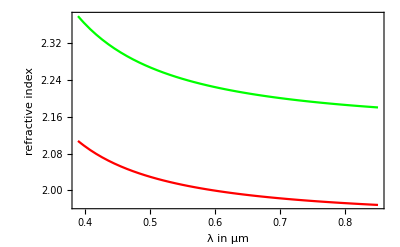

```mathematica
Plot[{nYVO[lam,20,o],nYVO[lam,20,e]},{lam,.39,.85},FrameLabel->{"λ in μm","refractive index"}]
```

### BBO

```mathematica
(* Sellmeier equations, BBO crystal *)
(* wavelength in µm *)
nBBO[lambda_,temp_,axis:(e|o)]:=Module[{nq,x},
nq=If[MatchQ[axis,o],
2.7359+0.01878/(lambda^2-0.01822)-0.01354*lambda^2,
2.3753+0.01224/(lambda^2-0.01667)-0.01516*lambda^2];
Sqrt[nq]+(InterpolatingPolynomial[If[MatchQ[axis,o],{{1.014,-16.64},{.579,-16.35},{.4047,-16.83}},{{1.014,-9.76},{.5790,-9.42},{.4047,-8.84}}],x]//.x->lambda)*10^-6*(temp-20)]
(*Refractive index of the extraordinary wave as a function of the polar angle (α) between optic axis and k vector*)
nBBOeo[λ_,temp_,θ_]:=nth[nBBO[λ,temp,o],nBBO[λ,temp,e],θ];
```

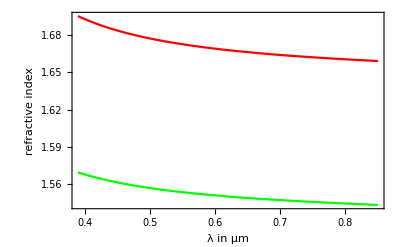

```mathematica
Plot[{nBBO[lam,20,o],nBBO[lam,20,e]},{lam,.39,.85},FrameLabel->{"λ in μm","refractive index"}]
```

## phase in single crystals

### phase difference in BBO crystal

```mathematica
ΔBBO = (koBBO-keBBO)*LBBO
```

(-keBBO+koBBO) LBBO

```mathematica
BBOkvect ={koBBO-> 2*π*nBBO[λ,TBBO,o]/λ,keBBO->2*π*nBBOeo[λ,TBBO,θp]/λ};
```

```mathematica
ϕBBO[θp_,λ_,LBBO_,TBBO_]:=Evaluate[(ΔBBO/. BBOkvect)];
```

### phase difference in YVO4 crystals

```mathematica
ΔYVO = (koYVO-keYVO)*LYVO
```

(-keYVO+koYVO) LYVO

```mathematica
YVOkvect ={koYVO-> 2*π*nYVO[λ,TYVO,o]/λ,keYVO->2*π*nYVOeo[λ,TYVO,θp]/λ};
```

```mathematica
ϕYVO[θp_,λ_,LYVO_,TYVO_]:=Evaluate[(ΔYVO/. YVOkvect)];
```

## phase compensation calculation examples

```mathematica
(* polarization state vector *)
pol[α_]:={Sin[α],Cos[α]};
(* phase between {1,0} (o-polarization) and {0,1} (e-polarization) vector *)
phasematrix[ϕ_]:={{1,0},{0,Exp[-I*ϕ]}};
```

```mathematica
IDet[αin_,αout_,ϕ_]:=Abs[pol[αout].phasematrix[ϕ].pol[αin]]^2;
IDetBBO[αin_,αout_,θp_,λ_,LBBO_,TBBO_]:=IDet[αin,αout,ϕBBO[θp,λ,LBBO,TBBO]];IDetYVO[αin_,αout_,θ_,λ_,LYVO_,TYVO_]:=IDet[αin,αout,ϕYVO[θ,λ,LYVO,TYVO]]
```

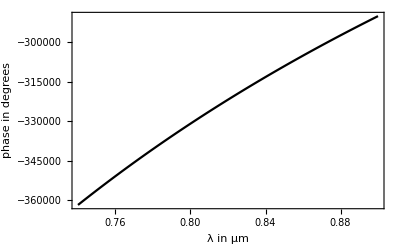

```mathematica
Plot[180/π(ϕYVO[θYVO,λ,LYVO,TYVO])/.{θYVO->π/2,LYVO->3440,TYVO->20} ,{λ,.740,.9},FrameLabel->{ "λ in µm","phase in degrees"},ImageSize->400,PlotRange->All]
```

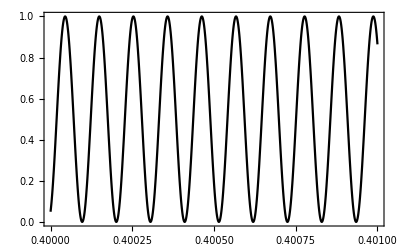

```mathematica
Plot[IDetYVO[αin,αout,θYVO,λ,LYVO,TYVO]/.{αin->π/4,αout->-π/4,θYVO->π/2,LYVO->3440,TYVO->20} ,{λ,.4,.401}]
```

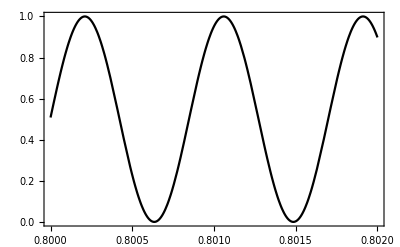

```mathematica
Plot[IDetYVO[αin,αout,θYVO,λ,LYVO,TYVO]/.{αin->π/4,αout->-π/4,θYVO->π/2,LYVO->3120,TYVO->20},{λ,.8,.802}]
```